# Test of Model Predictions

This Notebook shows how REAP can be used to test how the predictions of a given model change during the RG evolution to low energy.

```mathematica
If[$VersionNumber<6,
Get["Graphics`FilledPlot`"];
Get["Graphics`Colors`"],
ForestGreen=RGBColor[0.1,0.75,0.2];
];
```

```mathematica
Needs["REAP`RGEMSSM`"];
Needs["REAP`RGEPlotUtilities`"];
```

Loading REAP 1.11

SM0N: Two loop RG equation of κ not implemented yet.

SM: Two loop RG equations of Yν, Mνr and κ not implemented yet.

```mathematica
MZ=91.12;
GUT=2 10^16;
```

RGEReset is used in order to set all variables of RGESolver to their default values, if the notebook is executed several times.

```mathematica
RGEReset[];
```

## Definition of the model

We assume a supersymmetric model.  Below the SUSY-breaking scale (taken to be 1 TeV), the SM is used as an effective theory.

```mathematica
RGEReset[]
```

```mathematica
RGEAdd["MSSM",RGEtanβ->50,RGESearchTransitions->True];
RGEAdd["SM",RGECutoff->1000];
```

All couplings are given explicitly and no default values of the REAP package are used. The Yukawa couplings are given in "RL convention".  The neutrino masses are determined by Y_νand M.
κ is set to 0. In a type II see-saw scenario, κ is different from 0 below the mass threshold of the Higgs triplet.

```mathematica
RGESetInitial[GUT,
RGEg1->0.7044,
RGEg2->0.6965,
RGEg3->0.6984,
RGEYu->({{5.980 10^-6, 0, 0}, {0, 0.001736, 0}, {0, 0, 0.7417}}),
RGEYd->({{0.0007314, 0.001558+0.000022 ⅈ, 0.0002393+0.0006778 ⅈ}, {0.001555-0.000022ⅈ, 0.007555, 0.008913-0.000004 ⅈ}, {0.0002393-0.0006778 ⅈ, 0.008913+0.000004 ⅈ, 0.2872}}),
RGEYe->({{0.00009344, 0, 0}, {0, 0.01972, 0}, {0, 0, 0.33678}}),

RGEYν->0.5 ({{0.01, 0, 0}, {0.0001ⅈ, 0.1, 0}, {0, 0, 1}}),
RGEκ->({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}}),
RGEMνr->({{-3.660 10^10, 1.675 10^10, -1.675 10^11}, {1.675 10^10, -2.218 10^12, 1.098 10^13}, {-1.675 10^11, 1.098 10^13, -2.218 10^14}})

];
```

```mathematica
RGESolve[MZ,GUT];
```

## Plots

### Definitions

Define the plot region

```mathematica
ClearAll[tmin,tmax];
tmin=Log[10,MZ];
tmax=Log[10,GUT];
```

Define the functions that should be plotted

```mathematica
ClearAll[Mnu,Ye];
Mnu[mu_]:=RGEGetSolution[mu,RGEMν]//Chop
Ye[mu_]:=RGEGetSolution[mu,RGEYe]//Chop

ClearAll[MixingPars,MixingParsLogScale,NuMasses,NuMassesLogScale]
MixingPars[mu_]:=MNSParameters[Mnu[mu],Ye[mu]]⟦1⟧
MixingParsLogScale[x_]:=MixingPars[10^x]
NuMasses[mu_]:=MNSParameters[Mnu[mu],Ye[mu]]⟦2⟧
NuMassesLogScale[x_]:=NuMasses[10^x]

ClearAll[θ12,θ13,θ23,δ,φ1,φ2,m1,m2,m3,Δm2sol,Δm2atm]
θ12[t_]:=MixingParsLogScale[t]⟦1⟧/Degree
θ13[t_]:=MixingParsLogScale[t]⟦2⟧/Degree
θ23[t_]:=MixingParsLogScale[t]⟦3⟧/Degree
δ[t_]:=MixingParsLogScale[t]⟦4⟧/Degree
φ1[t_]:=MixingParsLogScale[t]⟦8⟧/Degree
φ2[t_]:=MixingParsLogScale[t]⟦9⟧/Degree
m1[t_]:=NuMassesLogScale[t]⟦1⟧
m2[t_]:=NuMassesLogScale[t]⟦2⟧
m3[t_]:=NuMassesLogScale[t]⟦3⟧
Δm2sol[t_]:=m2[t]^2-m1[t]^2
Δm2atm[t_]:=m3[t]^2-m2[t]^2
```

Test for compatibility with the experimental data
(allowed regions at the 3σ CL as given in Maltoni et al., hep-ph/0405172v4)

```mathematica
ClearAll[CompareToExperiment,IsCompatibleWithExp];
CompareToExperiment[t_]:=Module[{lNotComp,lComp},
lComp={};
lNotComp={};
If[Sin[θ12[t] Degree]^2≥0.23&&Sin[θ12[t] Degree]^2≤0.38,lComp=Append[lComp,"θ12"],lNotComp=Append[lNotComp,"θ12"]];
If[Sin[θ13[t] Degree]^2≤0.051,lComp=Append[lComp,"θ13"],lNotComp[lNotComp,"θ13"]];
If[Sin[θ23[t] Degree]^2≥0.34&&Sin[θ23[t] Degree]^2≤0.68,lComp=Append[lComp,"θ23"],lNotComp=Append[lNotComp,"θ23"]];If[Abs[Δm2atm[t]]≥1.3 10^-3&&Abs[Δm2atm[t]]≤3.2 10^-3,lComp=Append[lComp,"Δm2atm"],lNotComp=Append[lNotComp,"Δm2atm"]];
If[Δm2sol[t]≥7.1 10^-5&&Δm2sol[t]≤8.9 10^-5,lComp=Append[lComp,"Δm2sol"],lNotComp=Append[lNotComp,"Δm2sol"]];
Print["The following parameters are compatible with the experimental data at the 3σ CL:",lComp];
If[Length[lNotComp]==0,Return[1],Return[0]];
];
IsCompatibleWithExp:=CompareToExperiment[Log[10,MZ]]
```

Positions of the thresholds

```mathematica
ClearAll[M1,M2,M3,ShadowEFT]
{M1,M2,M3}=RGEGetTransitions[]⟦{4,3,2},1⟧;
ShadowEFT=RGEShadowEFT[M1,M2,M3,10^17];
```

### Compatibility to the experimental data

```mathematica
IsCompatibleWithExp;
```

The following parameters are compatible with the experimental data at the 3σ CL:{θ12,θ13,θ23,Δm2atm,Δm2sol}

The low energy parameters are

```mathematica
Print["θ_12(M_Z)=",θ12[Log[10,MZ]],"°"];
Print["θ_13(M_Z)=",θ13[Log[10,MZ]],"°"];
Print["θ_23(M_Z)=",θ23[Log[10,MZ]],"°"];
Print["(Δm^2)_atm(M_Z)=",Δm2atm[Log[10,MZ]],"eV^2"];
Print["(Δm^2)_sol(M_Z)=",Δm2sol[Log[10,MZ]],"eV^2"];
Print["m_1(M_Z)=",m1[Log[10,MZ]],"eV"];
Print["m_2(M_Z)=",m2[Log[10,MZ]],"eV"];
Print["m_3(M_Z)=",m3[Log[10,MZ]],"eV"];
```

θ_12(M_Z)=32.4948°

θ_13(M_Z)=0.100853°

θ_23(M_Z)=46.962°

(Δm^2)_atm(M_Z)=0.002093eV^2

(Δm^2)_sol(M_Z)=0.0000772044eV^2

m_1(M_Z)=0.0148434eV

m_2(M_Z)=0.0172491eV

m_3(M_Z)=0.048893eV

### Mixing Angles

Draw the plot for the mixing angles

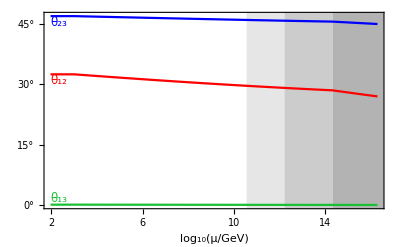

```mathematica
Show[Plot[
{θ12[t],θ13[t],θ23[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)",""},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*15,ToString[i*15]<>"°"},{i,0,3}],RGELogTicks[2,19],Table[{i*15,""},{i,0,3}]},
PlotRange->{All,All},PlotStyle->{Red,ForestGreen,Blue},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[θ, 12],FontColor->Red,FontSize->12],{tmin,θ12[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[θ, 13],FontColor->ForestGreen,FontSize->12],{tmin,θ13[tmin]},{-0.8,-1}],
Text[StyleForm[Subscript[θ, 23],FontColor->Blue,FontSize->12],{tmin,θ23[tmin]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

#### RG change of the angles:

```mathematica
Print["The RG change of θ_12 is :    θ_12(M_GUT)-θ_12(M_Z) = ",θ12[Log[10,GUT]]-θ12[Log[10,MZ]],"°"];
Print["The RG change of θ_13 is :    θ_13(M_GUT)-θ_13(M_Z) = ",θ13[Log[10,GUT]]-θ13[Log[10,MZ]],"°"];Print["The RG change of θ_23 is :    θ_23(M_GUT)-θ_23(M_Z) = ",θ23[Log[10,GUT]]-θ23[Log[10,MZ]],"°"];
```

The RG change of θ_12 is :    θ_12(M_GUT)-θ_12(M_Z) = -5.48665°

The RG change of θ_13 is :    θ_13(M_GUT)-θ_13(M_Z) = -0.0698569°

The RG change of θ_23 is :    θ_23(M_GUT)-θ_23(M_Z) = -1.96198°

### Phases

Draw the plot for the phases

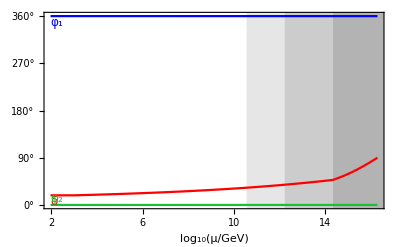

```mathematica
Show[Plot[
{δ[t],φ1[t],φ2[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)",""},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*45,ToString[i*45]<>"°"},{i,0,8}],RGELogTicks[2,19],Table[{i*45,""},{i,0,12}]},
PlotRange->{All,All},PlotStyle->{Red,Blue,ForestGreen},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[δ,FontColor->Red,FontSize->12],{tmin,δ[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[φ, 1],FontColor->Blue,FontSize->12],{tmin,φ1[tmin]},{-0.8,1.4}],
Text[StyleForm[Subscript[φ, 2],FontColor->ForestGreen,FontSize->12],{tmin,φ2[tmin]},{-0.8,-1}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

#### RG change of the phases:

```mathematica
Print["The RG change of δ is:   δ(M_GUT)-δ(M_Z) = ", δ[Log[10,GUT]]-δ[Log[10,MZ]],"°"];
Print["The RG change of φ_1 is:   φ_1(M_GUT)-φ_1(M_Z) = ", φ1[Log[10,GUT]]-φ1[Log[10,MZ]],"°"];
Print["The RG change of φ_2 is:   φ_2(M_GUT)-φ_2(M_Z) = ", φ2[Log[10,GUT]]-φ2[Log[10,MZ]],"°"];
```

The RG change of δ is:   δ(M_GUT)-δ(M_Z) = 71.6056°

The RG change of φ_1 is:   φ_1(M_GUT)-φ_1(M_Z) = -0.019962°

The RG change of φ_2 is:   φ_2(M_GUT)-φ_2(M_Z) = -0.00395842°

### Masses

#### mass eigenvalues

Draw the plot for the mass eigenvalues

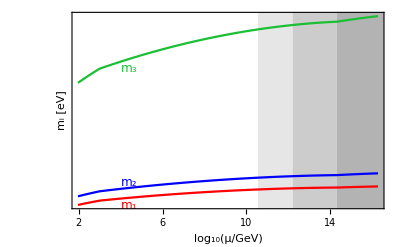

```mathematica
tlabel=4;   (* Position where the labels m1,m2,m3 should be placed *)
Show[Plot[
{m1[t],m2[t],m3[t]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","m_i [eV]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*0.01,PaddedForm[i*0.01,{3,2}]},{i,0,50}],RGELogTicks[2,19],Table[{i*0.01,""},{i,0,50}]},
PlotRange->{All,All},PlotStyle->{Red,Blue,ForestGreen},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[m, 1],FontColor->Red,FontSize->12],{tlabel,m1[tlabel]},{-0.8,1.4}],
Text[StyleForm[Subscript[m, 2],FontColor->Blue,FontSize->12],{tlabel,m2[tlabel]},{-0.8,-2}],
Text[StyleForm[Subscript[m, 3],FontColor->ForestGreen,FontSize->12],{tlabel,m3[tlabel]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

RG change of the masses:

```mathematica
Print["The RG change of m_1 is:   m_1(M_GUT)-m_1(M_Z) = ",m1[Log[10,GUT]]-m1[Log[10,MZ]]," eV"];
Print["The RG change of m_2 is:   m_2(M_GUT)-m_2(M_Z) = ",m2[Log[10,GUT]]-m2[Log[10,MZ]]," eV"];
Print["The RG change of m_3 is:   m_3(M_GUT)-m_3(M_Z) = ",m3[Log[10,GUT]]-m3[Log[10,MZ]]," eV"];
```

The RG change of m_1 is:   m_1(M_GUT)-m_1(M_Z) = 0.00515654 eV

The RG change of m_2 is:   m_2(M_GUT)-m_2(M_Z) = 0.00641555 eV

The RG change of m_3 is:   m_3(M_GUT)-m_3(M_Z) = 0.0186202 eV

#### mass squared differences

Draw the plot for the mass squared differences (on a logarithmic scale)

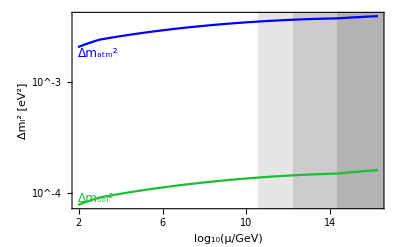

```mathematica
Show[Plot[
{Log[10,Abs[Δm2sol[t]]],Log[10,Abs[Δm2atm[t]]]},{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_i^2 [eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],RGELogTicksLabeledNegExp[-6,-1],RGELogTicks[2,19],RGELogTicks[-6,-1]},
PlotRange->{All,All},PlotStyle->{ForestGreen,Blue},
Prolog->{ShadowEFT},
Epilog->{
Text[StyleForm[Subscript[Δm, sol]^2,FontColor->ForestGreen,FontSize->12],{tmin,Log[10,Abs[Δm2sol[tmin]]]},{-0.8,-2}],
Text[StyleForm[Subscript[Δm, atm]^2,FontColor->Blue,FontSize->12],{tmin,Log[10,Abs[Δm2atm[tmin]]]},{-0.8,1.4}]},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

Draw the plot for the solar mass squared difference (on a linear scale)

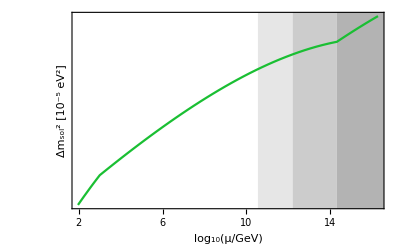

```mathematica
Show[Plot[
Δm2sol[t]*10^5,{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_sol^2 [10^-5 eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i,i},{i,-100,100}],RGELogTicks[2,19],Table[{i,""},{i,-100,100}]},
PlotRange->{All,All},PlotStyle->{ForestGreen},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

Draw the plot for the atmospheric mass squared difference (on a linear scale)

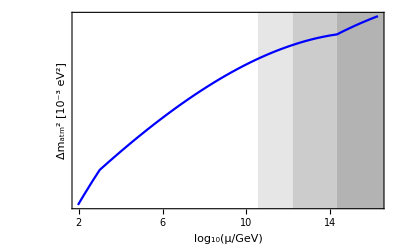

```mathematica
Show[Plot[
Δm2atm[t]*10^3,{t,tmin,tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","Δm_atm^2 [10^-3 eV^2]"},FrameTicks->{RGELogTicksLabeled[2,19],Table[{i*0.2,PaddedForm[i*0.2,{2,1}]},{i,-50,50}],RGELogTicks[2,19],Table[{i*0.2,""},{i,0,50}]},
PlotRange->{All,All},PlotStyle->{Blue},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

RG change of the mass squared differences:

```mathematica
Print["The RG change of (Δm^2)_sol is:     (Δm^2)_sol(M_GUT)-(Δm^2)_sol(M_Z) = ",Δm2sol[Log[10,GUT]]-Δm2sol[Log[10,MZ]]," eV^2"];
Print["The RG change of (Δm^2)_atm is:     (Δm^2)_atm(M_GUT)-(Δm^2)_atm(M_Z) = ",Δm2atm[Log[10,GUT]]-Δm2atm[Log[10,MZ]]," eV^2"];
```

The RG change of (Δm^2)_sol is:     (Δm^2)_sol(M_GUT)-(Δm^2)_sol(M_Z) = 0.0000828127 eV^2

The RG change of (Δm^2)_atm is:     (Δm^2)_atm(M_GUT)-(Δm^2)_atm(M_Z) = 0.00190502 eV^2

## CP asymmetry in leptogenesis

In order to calculate the CP asymmetry, the Majorana mass matrix of the right-handed and the left-handed neutrinos and the neutrino Yukawa couplings are needed. The returned matrices are the matrices which are valid at the given scale pScale. RGEMνr and RGEYν can also be used, but the returned matrices also contain the values of the right-handed neutrinos which are already integrated out.

In the following, the CP asymmetry (MSSM) in thermal leptogenesis in the limit M_1<< M_2,M_3is calculated. If you want to calculate the CP asymmetry in a different scenario, you have to change the formula appropiately.

```mathematica
ϵ[pScale_]:=Module[{lM,lY,lm,lvev},
(* right-handed neutrino mass matrix *)
lM=RGEGetSolution[pScale,RGERawMνr,1]; 

(* neutrino Yukawa couplings matrix *)
lY=RGEGetSolution[pScale,RGERawYν,1];

(* light neutrino mass matrix *)
lm=RGEGetSolution[pScale,RGEMν,1]*10^-9;

(* change to the basis, where M is diagonal *)
{lM,lY}=RGERotateM[lM,lY];

(* the mass of the lightest right-handed neutrino *)
lM1=lM⟦1,1⟧;

(* the Yukawa couplings of the lightest right-handed neutrino *)
lY1=lY⟦1⟧;

lvev=((N[RGEvEW*RGEtanβ/Sqrt[1+RGEtanβ^2]]/Sqrt[2])/.RGEGetOptions["MSSM"]⟦1,2⟧)/.RGEGetModelOptions["MSSM"]⟦1,2⟧;

(* CP asymmetry *)
leps=3/8/π*lM1/lvev^2*Im[(lY1.Conjugate[lm].lY1)]/(lY1.Conjugate[lY1]);

Return[leps];
];
```

```mathematica
RGEGetTransitions[]
```

{{∞,MSSM,{RGEtanβ→50}},{2.16263×10^14,MSSM,{RGEAutoGenerated→True,RGEIntegratedOut→1,RGEtanβ→50}},{1.66915×10^12,MSSM,{RGEAutoGenerated→True,RGEIntegratedOut→2,RGEtanβ→50}},{3.64295×10^10,MSSM0N,{RGEAutoGenerated→True,RGEtanβ→50}},{1000,SM0N,{RGEAutoGenerated→SM}}}

```mathematica
ϵ[RGEGetTransitions[]⟦4,1⟧]
```

3.38064×10^-10+0. ⅈ

However,the CP asymmetry in thermal leptogenesis (in the limit M_1<< M_2,M_3) is much easier obtained directly by RGEGetSolution.

```mathematica
RGEGetSolution[RGEGetTransitions[]⟦4,1⟧,RGEϵ1,1]
```

3.38064×10^-10+0. ⅈ

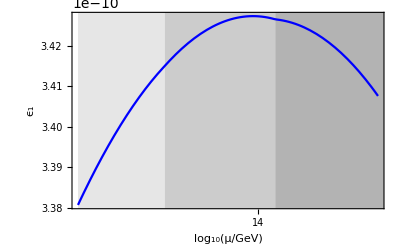

```mathematica
Show[Plot[RGEGetSolution[10^t,RGEϵ1],{t,Log[10,RGEGetTransitions[]⟦4,1⟧],tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","ϵ_1"},FrameTicks->{RGELogTicksLabeled[2,19],Automatic,RGELogTicks[2,19],Automatic},
PlotRange->{All,All},PlotStyle->{Blue},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```

Effective neutrino mass"(m̃)_1"

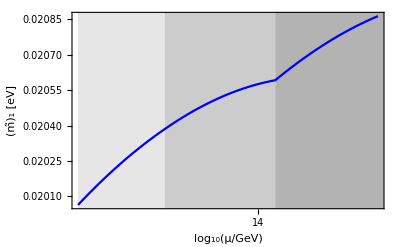

```mathematica
Show[Plot[
RGEGetSolution[10^t,RGEM1Tilde],{t,Log[10,RGEGetTransitions[]⟦4,1⟧],tmax},
ImageSize->400,FrameLabel->{"log_10(μ/GeV)","(m̃)_1 [eV]"},FrameTicks->{RGELogTicksLabeled[2,19],Automatic,RGELogTicks[2,19],Automatic},
PlotRange->{All,All},PlotStyle->{Blue},
Prolog->{ShadowEFT},
DisplayFunction->Identity
],DisplayFunction->$DisplayFunction]
```